```mathematica
(* First import the profiling data *)
SetDirectory[ParentDirectory[NotebookDirectory[]]];
data = Import[FileNameJoin[{ParentDirectory[],"malloc_out/ubench.tp_small/baseline/0/ubench.tp_small.prof.0.0"}],"List"];
```

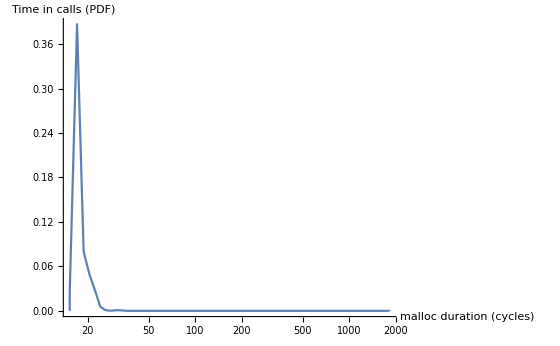

```mathematica
(* Plot profiling data for a given microbenchmark for a given function. *)
SmoothHistogram[data,ScalingFunctions->{"Log"},AxesLabel->{"malloc duration (cycles)","Time in calls (PDF)"},PlotRange->All]
```

```mathematica
(* Compute average # of cycles per call, tail latency? Should probably only do this for fast-path requests...*)
```

```mathematica
(* Plot the total # of cycles spent on malloc() calls on the fast path. *)
(* Plot % improvement in time spent on malloc() calls on the fast path. *)
nAvgCyclesBaseline={41.73642502,24.43354159,28.6228345,21.32489566,20.09140432,19.4238786};
nAvgCyclesRealistic={33.52091818,22.55035396,24.55678793,17.76965815,20.09574207,18.56360659};
percentSpeedups = 100*(nAvgCyclesBaseline -nAvgCyclesRealistic)/nAvgCyclesBaseline; 
stdDevCyclesBaseline={0,0,0,0,0,0};
stdDevCyclesRealistic={0,0,0,0,0,0};
(* TODO: Use std. dev's to calculate error bars *)
errorIntervals={0,0,0,0,0,0};
plotTitle="% speedup of fast-path malloc() & free() calls";
Labeled[BarChart[Around[percentSpeedups,errorIntervals],BarOrigin->Left,PlotLabel->plotTitle,ChartLabels->Placed[{"tp", "tp_small","sized_deletes","gauss","gauss_free","antagonist"},Left]],{"Fast path cycles improvement (%)"},{Bottom}]
```

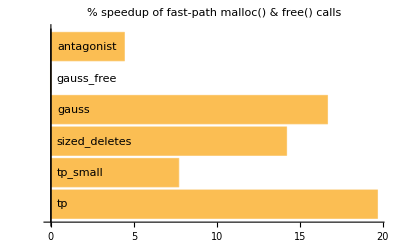
```mathematica
-Graphics-"Fast path cycles improvement (%)"
```